# Equazioni della dinamica di un’antenna di un radiotelescopio

-Graphics-

## Applicazione metodo Lagrange

### Definizione delle funzioni che costruiscono le matrici di trasformazione elementari

```mathematica
T[x_,y_,z_]:={{1,0,0,x} ,{0,1,0,y},{0,0,1,z},{0,0,0,1}}
```

```mathematica
Rz[x_]:= {{Cos[x],-Sin[x],0,0},{Sin[x],Cos[x],0,0},{0,0,1,0},{0,0,0,1}}
```

```mathematica
Rx[x_]:= {{1,0,0,0},{0,Cos[x],-Sin[x],0},{0,Sin[x],Cos[x],0},{0,0,0,1}}
```

```mathematica
Ry[x_] := {{Cos[x],0,Sin[x],0} ,{0,1,0,0},{-Sin[x],0,Cos[x],0},{0,0,0,1}};
```

### Costruzione delle trasformazioni fra sistemi di riferimento successivi (da sistema “0” a sistema “2”)

1) sistema di riferimento “1” solidale alla forcella, con origine nel baricentro della forcella G1. Traslato verticalmente di h1 rispetto al sistema “0”.

```mathematica
T01=T[0,0,h1].Rz[θ];T1=T01; MatrixForm@T1
```

(Cos[θ] | -Sin[θ] | 0 | 0
Sin[θ] | Cos[θ] | 0 | 0
0 | 0 | 1 | h1
0 | 0 | 0 | 1)

2) sistema di riferimento solidale alla parabola dell’antenna, il cui asse x contiene il baricentro della parabola G2.

```mathematica
T12=T[0,0,h2].Ry[-φ];T2=FullSimplify[T1.T12];MatrixForm@T2
```

(Cos[θ] Cos[φ] | -Sin[θ] | -Cos[θ] Sin[φ] | 0
Cos[φ] Sin[θ] | Cos[θ] | -Sin[θ] Sin[φ] | 0
Sin[φ] | 0 | Cos[φ] | h1+h2
0 | 0 | 0 | 1)

### Posizione delle origini dei sistemi di riferimento

```mathematica
O1=T1.{0,0,0,1};O1=Most[O1]
```

{0,0,h1}

```mathematica
O2=T2.{0,0,0,1};O2=Most[O2]
```

{0,0,h1+h2}

### Posizione dei due baricentri

```mathematica
G1=O1
```

{0,0,h1}

```mathematica
G2=T2.{h3,0,0,1};G2=Most[G2]
```

{h3 Cos[θ] Cos[φ],h3 Cos[φ] Sin[θ],h1+h2+h3 Sin[φ]}

### Rappresentazione grafica dei sistemi

```mathematica
PlotFrame[T_]:=Module[{O,X,Y,Z,l=2},
O=T[[1;;3,4]];
X=O+l T[[1;;3,1]];
Y=O+l T[[1;;3,2]];
Z=O+l T[[1;;3,3]];
Graphics3D[{Thick,Red, Arrow[{O,X}],Blue, Arrow[{O,Y}], Brown,Arrow[{O,Z}]}]
]
```

```mathematica
Manipulate[Block[{h1=6,h2=3,h3=2,θ=q1,φ=q2},Show[
Graphics3D[{
Orange,Thick,Line[{O1,O2}]
},PlotRange->{{-5,5},{-5,10},{0,15}}],
PlotFrame[T1],PlotFrame[T2]
]
],
{q1,0,π/2},{q2,0,π/2}
]
```

### Equazioni del moto usando l’energia cinetica di un corpo rigido

```mathematica
θ=q1[t]
```

q1[t]

```mathematica
φ=q2[t]
```

q2[t]

### Velocità angolari (in terna mobile)

#### Forcella

```mathematica
R1=T1[[1;;3,1;;3]];MatrixForm@R1
```

(Cos[q1[t]] | -Sin[q1[t]] | 0
Sin[q1[t]] | Cos[q1[t]] | 0
0 | 0 | 1)

```mathematica
mW1=FullSimplify[Transpose[R1].D[R1, t]]; MatrixForm[mW1]
```

(0 | -q1'[t] | 0
q1'[t] | 0 | 0
0 | 0 | 0)

```mathematica
ω1={mW1[[3,2]],mW1[[1,3]],mW1[[2,1]]}
```

{0,0,q1'[t]}

#### Parabola

```mathematica
R2=T2[[1;;3,1;;3]];MatrixForm@R2
```

(Cos[q1[t]] Cos[q2[t]] | -Sin[q1[t]] | -Cos[q1[t]] Sin[q2[t]]
Cos[q2[t]] Sin[q1[t]] | Cos[q1[t]] | -Sin[q1[t]] Sin[q2[t]]
Sin[q2[t]] | 0 | Cos[q2[t]])

```mathematica
mW2=FullSimplify[Transpose[R2].D[R2, t]]; MatrixForm[mW2]
```

(0 | -Cos[q2[t]] q1'[t] | -q2'[t]
Cos[q2[t]] q1'[t] | 0 | -Sin[q2[t]] q1'[t]
q2'[t] | Sin[q2[t]] q1'[t] | 0)

```mathematica
ω2={mW2[[3,2]],mW2[[1,3]],mW2[[2,1]]}
```

{Sin[q2[t]] q1'[t],-q2'[t],Cos[q2[t]] q1'[t]}

### Energie

#### Energia cinetica della forcella

```mathematica
Tf=FullSimplify[1/2 m1(D[G1, t]) .(D[G1, t])+1/2 ω1 .({{IGfx, 0, 0}, {0, IGfy, 0}, {0, 0, IGfz}}).ω1 ]
```

1/2 IGfz q1'[t]^2

#### Energia cinetica della parabola

```mathematica
Ta=FullSimplify[1/2 m2(D[G2, t]) .(D[G2, t])+1/2 ω2 .({{IGax, 0, 0}, {0, IGa, 0}, {0, 0, IGa}}).ω2 ]
```

1/4 ((IGa+IGax+h3^2 m2+(IGa-IGax+h3^2 m2) Cos[2 q2[t]]) q1'[t]^2+2 (IGa+h3^2 m2) q2'[t]^2)

Simmetrico rispetto a x perchè ruota su x quindi Igy = Igz

#### Energia Potenziale rispetto al baricentro

```mathematica
V=FullSimplify[m1 g G1[[3]]+m2 g G2[[3]]]
```

g h1 m1+g m2 (h1+h2+h3 Sin[q2[t]])

#### Lagrangiana

```mathematica
L=Tf+Ta-V
```

-g h1 m1-g m2 (h1+h2+h3 Sin[q2[t]])+1/2 IGfz q1'[t]^2+1/4 ((IGa+IGax+h3^2 m2+(IGa-IGax+h3^2 m2) Cos[2 q2[t]]) q1'[t]^2+2 (IGa+h3^2 m2) q2'[t]^2)

#### Calcolo la Potenza Virtuale

```mathematica
W=M1 q1'[t]+M2 q2'[t]+Fv D[G2[[1]], t]
```

M1 q1'[t]+M2 q2'[t]+Fv (-h3 Cos[q2[t]] Sin[q1[t]] q1'[t]-h3 Cos[q1[t]] Sin[q2[t]] q2'[t])

#### Forze Generalizzate non conservative

```mathematica
Q1=Coefficient[W,q1'[t]]
```

M1-Fv h3 Cos[q2[t]] Sin[q1[t]]

```mathematica
Q2=Coefficient[W,q2'[t]]
```

M2-Fv h3 Cos[q1[t]] Sin[q2[t]]

### Equazioni di Lagrange

```mathematica
eq1=FullSimplify[D[D[L, q1'[t]], t]-D[L, q1[t]]]==Q1
```

-(IGa-IGax+h3^2 m2) Sin[2 q2[t]] q1'[t] q2'[t]+1/2 (IGa+IGax+2 IGfz+h3^2 m2+(IGa-IGax+h3^2 m2) Cos[2 q2[t]]) q1''[t]==M1-Fv h3 Cos[q2[t]] Sin[q1[t]]

```mathematica
eq2=FullSimplify[D[D[L, q2'[t]], t]-D[L, q2[t]]]==Q2
```

g h3 m2 Cos[q2[t]]+(IGa-IGax+h3^2 m2) Cos[q2[t]] Sin[q2[t]] q1'[t]^2+(IGa+h3^2 m2) q2''[t]==M2-Fv h3 Cos[q1[t]] Sin[q2[t]]

```mathematica
sol=FullSimplify@Solve[{eq1,eq2},{M1,M2}]
```

{{M1→Fv h3 Cos[q2[t]] Sin[q1[t]]-(IGa-IGax+h3^2 m2) Sin[2 q2[t]] q1'[t] q2'[t]+1/2 (IGa+IGax+2 IGfz+h3^2 m2+(IGa-IGax+h3^2 m2) Cos[2 q2[t]]) q1''[t],M2→h3 (g m2 Cos[q2[t]]+Fv Cos[q1[t]] Sin[q2[t]])+(IGa-IGax+h3^2 m2) Cos[q2[t]] Sin[q2[t]] q1'[t]^2+(IGa+h3^2 m2) q2''[t]}}

```mathematica
solM1=M1/.sol[[1,1]]/.{q1'[t]->q10,q1''[t]->0,q2[t]->q20,q2'[t]->0}
```

Fv h3 Cos[q20] Sin[q1[t]]

```mathematica
solM2=Simplify[M2/.sol[[1,2]]/.{q1'[t]->q10,q1''[t]->0,q2[t]->q20,q2'[t]->0,q2''[t]->0}]
```

Fv h3 Cos[q1[t]] Sin[q20]+Cos[q20] (g h3 m2+(IGa-IGax+h3^2 m2) q10^2 Sin[q20])

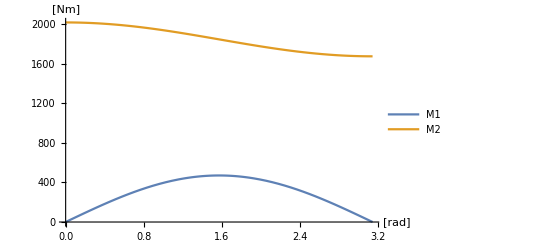

```mathematica
Block[{Fv=250,h3=2,q20=20°,g=9.81,m2=100,IGa=0,IGax=0,q10=0},Plot[{solM1,solM2},{q1[t],0,π},AxesLabel->{"[rad]","[Nm]"},PlotLegends->{"M1","M2"}]]
```

## Applicazione metodo Newton-Eulero

Per scrivere le equazioni di Newton-Eulero occorre specificare la posizione dei corpi e dei punti di applicazione delle forze in funzione delle coordinate generalizzate.
E’ noto che la forza vento agisce esattamente nel baricentro del corpo 2.

### Momenti delle forze rispetto ai baricentri

Si definiscono i momenti dati dalle reazioni vincolari rispetto ai due baricentri. Le reazioni Vincolari sono espresse rispetto al sistema di riferimento 1.
Momento rispetto al baricentro G1 delle reazioni vincolari alla base della forcella

```mathematica
MRAG1=G1×{RAx,RAy,RAz}
```

{-h1 RAy,h1 RAx,0}

Esprimo il momento ottenuto nel sistema di riferimento 1 per la successiva scrittura delle equazioni di Eulero.

```mathematica
MRAG101=Transpose[T1[[1;;3,1;;3]]].MRAG1
```

{-h1 RAy Cos[q1[t]]+h1 RAx Sin[q1[t]],h1 RAx Cos[q1[t]]+h1 RAy Sin[q1[t]],0}

Momento rispetto al baricentro G1 delle reazioni vincolari sussistenti tra antenna e forcella.

```mathematica
MRBG1=(O2-G1)×{-RBx,-RBy,-RBz}
```

{h2 RBy,-h2 RBx,0}

Esprimo il momento ottenuto nel sistema di riferimento 1 per la successiva scrittura delle equazioni di Eulero.

```mathematica
MRBG101=Transpose[T1[[1;;3,1;;3]]].MRBG1
```

{h2 RBy Cos[q1[t]]-h2 RBx Sin[q1[t]],-h2 RBx Cos[q1[t]]-h2 RBy Sin[q1[t]],0}

Momento rispetto al baricentro G2 delle reazioni vincolari sussistenti tra antenna e forcella:
(Viene gia applicato il principio di Azione-Reazione)

```mathematica
MRBG2=(O2-G2)×{RBx,RBy,RBz}
```

{-h3 RBz Cos[q2[t]] Sin[q1[t]]+h3 RBy Sin[q2[t]],h3 RBz Cos[q1[t]] Cos[q2[t]]-h3 RBx Sin[q2[t]],-h3 RBy Cos[q1[t]] Cos[q2[t]]+h3 RBx Cos[q2[t]] Sin[q1[t]]}

Esprimo il momento ottenuto nel sistema di riferimento 2 per la successiva scrittura delle equazioni di Eulero.

```mathematica
MRBG202=Transpose[T2[[1;;3,1;;3]]].MRBG2
```

{(-h3 RBy Cos[q1[t]] Cos[q2[t]]+h3 RBx Cos[q2[t]] Sin[q1[t]]) Sin[q2[t]]+Cos[q2[t]] Sin[q1[t]] (h3 RBz Cos[q1[t]] Cos[q2[t]]-h3 RBx Sin[q2[t]])+Cos[q1[t]] Cos[q2[t]] (-h3 RBz Cos[q2[t]] Sin[q1[t]]+h3 RBy Sin[q2[t]]),Cos[q1[t]] (h3 RBz Cos[q1[t]] Cos[q2[t]]-h3 RBx Sin[q2[t]])-Sin[q1[t]] (-h3 RBz Cos[q2[t]] Sin[q1[t]]+h3 RBy Sin[q2[t]]),Cos[q2[t]] (-h3 RBy Cos[q1[t]] Cos[q2[t]]+h3 RBx Cos[q2[t]] Sin[q1[t]])-Sin[q1[t]] Sin[q2[t]] (h3 RBz Cos[q1[t]] Cos[q2[t]]-h3 RBx Sin[q2[t]])-Cos[q1[t]] Sin[q2[t]] (-h3 RBz Cos[q2[t]] Sin[q1[t]]+h3 RBy Sin[q2[t]])}

### Equazioni di Newton-Eulero

#### Corpo 1 Supporto

```mathematica
e1x=m1 D[D[G1[[1]], t], t]==RAx-RBx
```

0==RAx-RBx

```mathematica
e1y=m1 D[D[G1[[2]], t], t]==RAy-RBy
```

0==RAy-RBy

```mathematica
e1z=m1 D[D[G1[[3]], t], t]==RAz-RBz-m1 g
```

0==-g m1+RAz-RBz

Il vincolo inferiore nel corpo 1 permette soltanto la rotazione attorno a z, definisco quindi i Momenti di reazione rispetto al sistema 1

```mathematica
MA = {MAx,MAy,0};
```

Il vincolo superiore nel corpo 2 permette soltanto la rotazione attorno a y, definisco quindi i Momenti di reazione rispetto al sistema 1

```mathematica
MB={MBx,0,MBz};
```

```mathematica
e1θx=0==MRAG101[[1]]+MRBG101[[1]]+MA[[1]]-MB[[1]]
```

0==MAx-MBx-h1 RAy Cos[q1[t]]+h2 RBy Cos[q1[t]]+h1 RAx Sin[q1[t]]-h2 RBx Sin[q1[t]]

```mathematica
e1θy=0==MRAG101[[2]]+MRBG101[[2]]+M2+MA[[2]]
```

0==M2+MAy+h1 RAx Cos[q1[t]]-h2 RBx Cos[q1[t]]+h1 RAy Sin[q1[t]]-h2 RBy Sin[q1[t]]

```mathematica
e1θz=IGfz D[ω1[[3]], t] ==MRAG101[[3]]+MRBG101[[3]]+M1-MB[[3]]
```

IGfz q1''[t]==M1-MBz

#### Corpo 2 Parabola

```mathematica
e2x=FullSimplify[m2 D[D[G2[[1]], t], t]==RBx+Fv]
```

Fv+RBx+h3 m2 Cos[q2[t]] (Cos[q1[t]] (q1'[t]^2+q2'[t]^2)+Sin[q1[t]] q1''[t])+h3 m2 Sin[q2[t]] (-2 Sin[q1[t]] q1'[t] q2'[t]+Cos[q1[t]] q2''[t])==0

```mathematica
e2y=FullSimplify[m2 D[D[G2[[2]], t], t]==RBy]
```

h3 m2 (Cos[q1[t]] (-2 Sin[q2[t]] q1'[t] q2'[t]+Cos[q2[t]] q1''[t])-Sin[q1[t]] (Cos[q2[t]] (q1'[t]^2+q2'[t]^2)+Sin[q2[t]] q2''[t]))==RBy

```mathematica
e2z=FullSimplify[m2 D[D[G2[[3]], t], t]==RBz-m2 g]
```

m2 (g-h3 Sin[q2[t]] q2'[t]^2+h3 Cos[q2[t]] q2''[t])==RBz

Il Momento di reazione MB deve essere riferito rispetto al corpo 2

```mathematica
MB12=Transpose[T12[[1;;3,1;;3]]].MB
```

{MBx Cos[q2[t]]+MBz Sin[q2[t]],0,MBz Cos[q2[t]]-MBx Sin[q2[t]]}

```mathematica
e2φx=FullSimplify[IGax D[ω2[[1]], t]==MRBG202[[1]]+MB12[[1]]]
```

Cos[q2[t]] (MBx-IGax q1'[t] q2'[t])+Sin[q2[t]] (MBz-IGax q1''[t])==0

```mathematica
e2φy=Simplify[IGa D[ω2[[2]], t]-(IGa-IGax)ω2[[3]]ω2[[1]]==MRBG202[[2]]-M2]
```

M2+h3 RBx Cos[q1[t]] Sin[q2[t]]+h3 RBy Sin[q1[t]] Sin[q2[t]]==h3 RBz Cos[q2[t]]+(IGa-IGax) Cos[q2[t]] Sin[q2[t]] q1'[t]^2+IGa q2''[t]

```mathematica
e2φz=Simplify[IGa D[ω2[[3]], t]-(IGax-IGa)ω2[[1]]ω2[[2]]==MRBG202[[3]]+MB12[[3]]]
```

h3 RBy Cos[q1[t]]+MBx Sin[q2[t]]+IGa Cos[q2[t]] q1''[t]==MBz Cos[q2[t]]+h3 RBx Sin[q1[t]]+(2 IGa-IGax) Sin[q2[t]] q1'[t] q2'[t]

#### Risoluzione

```mathematica
Reazioni=Simplify@Solve[{e1x,e1y,e1z,e2x,e2y,e2z,e1θx,e1θy,e1θz,e2φx,e2φy,e2φz},{RAx,RAy,RAz,RBx,RBy,RBz,MAx,MAy,MBx,MBz,M1,M2}];
```

```mathematica
SolM1=FullSimplify[M1/.Reazioni/.{q1'[t]->q10,q1''[t]->0,q2[t]->q20,q2'[t]->0}]
```

{Fv h3 Cos[q20] Sin[q1[t]]}

```mathematica
SolM2 = First@FullSimplify[M2/.Reazioni/.{q1'[t]->q10,q1''[t]->0,q2[t]->q20,q2'[t]->0,q2''[t]->0}]
```

Fv h3 Cos[q1[t]] Sin[q20]+Cos[q20] (g h3 m2+(IGa-IGax+h3^2 m2) q10^2 Sin[q20])